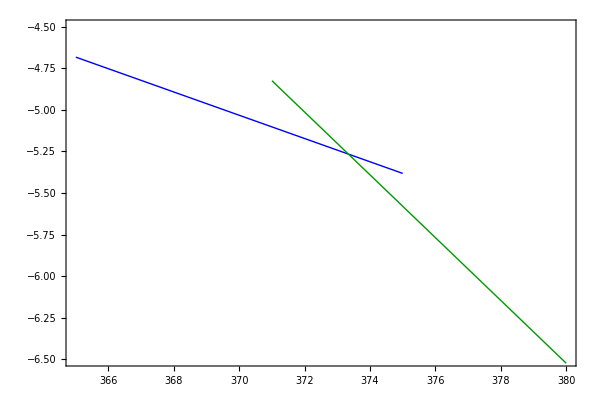

```mathematica
Module[{Sl,Sv,Ss,Gl,Gv,Gs,T0,μT,colS,colL,colV,SolidLiquid,LiquidVapor},
Sl=69.9 ;Sv=188.7;Ss=44.8;(*J/mol/K*)
Gl=0;Gv=8950;Gs=590;(*J/mol*)

T0=298;
μT[T_,S_,ΔG_]:=(-S*(T-T0)+ΔG)/1000;

colS=Magenta;colL=Blue;colV=RGBColor[0,0.6,0];

SolidLiquid=Show[
Plot[μT[T,Ss,Gs],{T,270,277},PlotStyle->{Thick,colS}],
Plot[μT[T,Sl,Gl],{T,273,280},PlotStyle->{Thick,colL}],
PlotRange->{{270,280},{1.2,1.9}},Axes->False,Frame->True,FrameTicks->True,LabelStyle->{17,Black},ImageSize->{600,400},AspectRatio->Full];

LiquidVapor=Show[
Plot[μT[T,Sl,Gl],{T,365,375},PlotStyle->{Thick,colL}],
Plot[μT[T,Sv,Gv],{T,371,380},PlotStyle->{Thick,colV}],
PlotRange->{{365,380},{-6.5,-4.5}},Axes->False,Frame->True,FrameTicks->True,LabelStyle->{17,Black},ImageSize->{600,400},AspectRatio->Full]
]
```